```mathematica
2-2
```

0

# Random Walks on the Plane

Nicholas Wheeler
30 August 2011

### Introduction

The following material is quoted from "Simulated Random Walks" (Notebook dated 4 April 2008)

### Steps of unit length, random turn angles uniformly distributed

The following commands generate the steps that contribute to a population  of four such 1000-step walks:

```mathematica
Steps1=Table[{Cos[α], Sin[α]}/.{α->2π RandomReal[]},{n,1,1000}];
Steps2=Table[{Cos[α], Sin[α]}/.{α->2π RandomReal[]},{n,1,1000}];
Steps3=Table[{Cos[α], Sin[α]}/.{α->2π RandomReal[]},{n,1,1000}];
Steps4=Table[{Cos[α], Sin[α]}/.{α->2π RandomReal[]},{n,1,1000}];
```

Here is a typical step

```mathematica
Part[Steps1, 137]
```

{-0.878423,-0.477883}

and here is a demonstration that (like all others) it has unit length:

```mathematica
Norm[%]
```

1.

The following commands list the successive positions achieved by the k^th walker:

```mathematica
SuccessivePositions1=Table[∑_(k=1)^m Steps1⟦k⟧, {m,1,1000}];
SuccessivePositions2=Table[∑_(k=1)^m Steps2⟦k⟧, {m,1,1000}];
SuccessivePositions3=Table[∑_(k=1)^m Steps3⟦k⟧, {m,1,1000}];
SuccessivePositions4=Table[∑_(k=1)^m Steps4⟦k⟧, {m,1,1000}];
```

Here are I construct and draw graphic displays of the paths traced by the respective walkers:

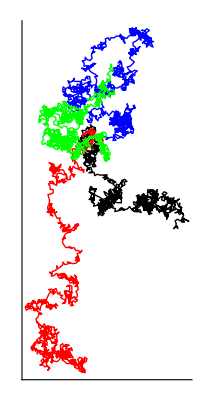

```mathematica
RandomWalk1=Graphics[{Black,Line[SuccessivePositions1]}];
RandomWalk2=Graphics[{Red,Line[SuccessivePositions2]}];
RandomWalk3=Graphics[{Blue,Line[SuccessivePositions3]}];
RandomWalk4=Graphics[{Green,Line[SuccessivePositions4]}];

Show[RandomWalk1,RandomWalk2,RandomWalk3,RandomWalk4, Axes->True, Ticks->False]
```

Theoretically, we expect the average displacement achieved after N steps to grow as √N. That expectation informs the design of the following figure

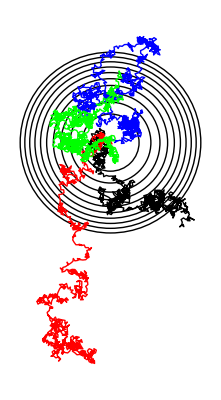

```mathematica
CircularGrid=Graphics[{Circle[{0,0},√100],Circle[{0,0},√200],Circle[{0,0},√300],Circle[{0,0},√400],Circle[{0,0},√500],Circle[{0,0},√600],Circle[{0,0},√700],Circle[{0,0},√800],Circle[{0,0},√900],Circle[{0,0},√1000]}];

Show[CircularGrid, RandomWalk1, RandomWalk2, RandomWalk3, RandomWalk4]
```

We  compute and display the evolving net displacement from the origin achieved by the respective walkers, and compare it to the theoretical expectation:

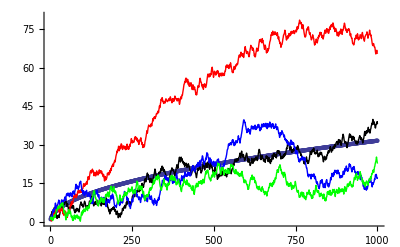

```mathematica
NetDisplacement1[n_]:=Norm[Part[SuccessivePositions1,n]]
NetDisplacement2[n_]:=Norm[Part[SuccessivePositions2,n]]
NetDisplacement3[n_]:=Norm[Part[SuccessivePositions3,n]]
NetDisplacement4[n_]:=Norm[Part[SuccessivePositions4,n]]

PlotNetDisplacement1=ListPlot[Table[NetDisplacement1[n],{n,1,1000}], Joined->True, PlotStyle->Black, PlotRange->{0,80}];
PlotNetDisplacement2=ListPlot[Table[NetDisplacement2[n],{n,1,1000}], Joined->True, PlotStyle->Red, PlotRange->{0,80}];
PlotNetDisplacement3=ListPlot[Table[NetDisplacement3[n],{n,1,1000}], Joined->True, PlotStyle->Blue, PlotRange->{0,80}];
PlotNetDisplacement4=ListPlot[Table[NetDisplacement4[n],{n,1,1000}], Joined->True, PlotStyle->Green, PlotRange->{0,80}];

ExpectedNetDisplacement=ListPlot[Table[√n,{n,1,1000}], PlotRange->{0,80}];

Show[ExpectedNetDisplacement,PlotNetDisplacement1 ,PlotNetDisplacement2,PlotNetDisplacement3,PlotNetDisplacement4]
```

#### Normal diffusion

Let

ρ[x, y, N]dx dy=

describe the fraction of a very large population  of walkers who, after N steps, find themselves in the neighborhood [dx, dy] of the point [x, y]. Random walk theory leads to the conclusion that ρ[x, y, N] has the form of a simple bivariate normal distribution function

```mathematica
ρ[x_, y_, N_]:=(ⅇ^(-(x^2+y^2)/(2N)))/(N √(2 π))
```

and satisfies the diffusion equation

1/2(∂_(x,x) +∂_(y,y))ρ=∂_N ρ

which I verify:

```mathematica
1/2(D[ρ[x,y,N],{x,2}]+D[ρ[x,y,N],{y,2}])==D[ρ[x,y,N],{N,1}]//Simplify
```

True

Here is a 3D display of the  evolving density function

```mathematica
Manipulate[Plot3D[ρ[x,y,N],{x,-√3000,√3000},{y,-√3000,√3000}, PlotRange->{0,0.004}],{N,100,1000,100}]
```

REMARK: It would take the data derived from VERY MANY WALKS (Avogadro's Number^(2/3)?) to establish this result numerically, though in one dimension one needs far fewer than  Avogadro's Number^(1/3) ~ 10^8 to obtain convincing results.

### Superdiffusion: Levy Flights

Let step length be statistically determined. Let it, in particular, be determined by a distribution with a very "long tail," so that occasional steps are exceptionally long. Such random walks (or "flights") are used to gain insight into the mechanism that underlies the departures from the "law of diffusion" that are encountered in a wide assortment of physical (+ biological, financial) applications.

To illustrate the point, I adopt the distribution law

```mathematica
Levy[x_]:=PDF[FRatioDistribution[3,3.9999],x]
```

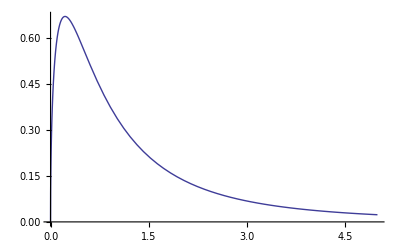

```mathematica
Plot[Levy[x],{x,0,5}]
```

The long tail—evident in the figure—is so long that the variance is indeterminate:

```mathematica
Mean[FRatioDistribution[3,3.9999]]
Variance[FRatioDistribution[3,3.9999]]
```

2.00005

Indeterminate

I remark in passing that the similar-looking long-tail distribution

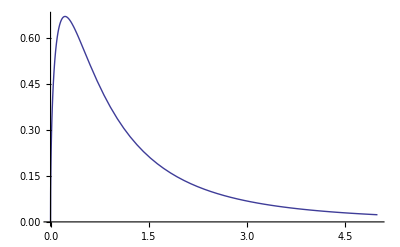

```mathematica
Plot[PDF[FRatioDistribution[3,4.0001],x],{x,0,5}]
```

possesses a large but finite variance:

```mathematica
Mean[FRatioDistribution[3,4.0001]]
Variance[FRatioDistribution[3,4.0001]]
```

1.99995

133329.

Proceeding now very much as before, we construct

```mathematica
LevySteps1=Table[r{Cos[α], Sin[α]}/.{r->RandomReal[FRatioDistribution[3,3.9999]],α->2π RandomReal[]},{n,1,1000}];
LevySteps2=Table[r{Cos[α], Sin[α]}/.{r->RandomReal[FRatioDistribution[3,3.9999]],α->2π RandomReal[]},{n,1,1000}];
LevySteps3=Table[r{Cos[α], Sin[α]}/.{r->RandomReal[FRatioDistribution[3,3.9999]],α->2π RandomReal[]},{n,1,1000}];
LevySteps4=Table[r{Cos[α], Sin[α]}/.{r->RandomReal[FRatioDistribution[3,3.9999]],α->2π RandomReal[]},{n,1,1000}];
```

```mathematica
SuccessiveLevyPositions1=Table[∑_(k=1)^m LevySteps1⟦k⟧, {m,1,1000}];
SuccessiveLevyPositions2=Table[∑_(k=1)^m LevySteps2⟦k⟧, {m,1,1000}];
SuccessiveLevyPositions3=Table[∑_(k=1)^m LevySteps3⟦k⟧, {m,1,1000}];
SuccessiveLevyPositions4=Table[∑_(k=1)^m LevySteps4⟦k⟧, {m,1,1000}];
```

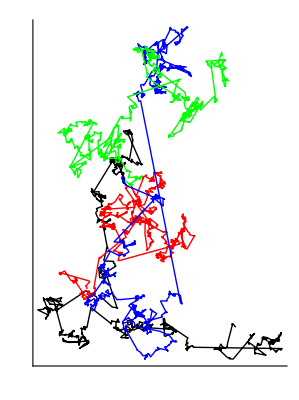

```mathematica
LevyFlight1=Graphics[{Black,Line[SuccessiveLevyPositions1]}];
LevyFlight2=Graphics[{Red,Line[SuccessiveLevyPositions2]}];
LevyFlight3=Graphics[{Blue,Line[SuccessiveLevyPositions3]}];
LevyFlight4=Graphics[{Green,Line[SuccessiveLevyPositions4]}];

Show[LevyFlight1,LevyFlight2,LevyFlight3,LevyFlight4, Axes->True, Ticks->False]
```

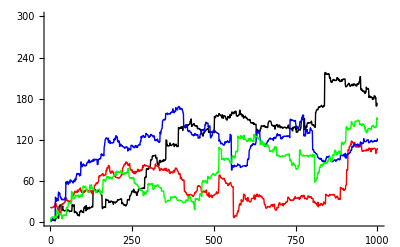

```mathematica
NetLevyDisplacement1[n_]:=Norm[Part[SuccessiveLevyPositions1,n]]
NetLevyDisplacement2[n_]:=Norm[Part[SuccessiveLevyPositions2,n]]
NetLevyDisplacement3[n_]:=Norm[Part[SuccessiveLevyPositions3,n]]
NetLevyDisplacement4[n_]:=Norm[Part[SuccessiveLevyPositions4,n]]

PlotNetLevyDisplacement1=ListPlot[Table[NetLevyDisplacement1[n],{n,1,1000}], Joined->True, PlotStyle->Black, PlotRange->{0,300}];
PlotNetLevyDisplacement2=ListPlot[Table[NetLevyDisplacement2[n],{n,1,1000}], Joined->True, PlotStyle->Red, PlotRange->{0,300}];
PlotNetLevyDisplacement3=ListPlot[Table[NetLevyDisplacement3[n],{n,1,1000}], Joined->True, PlotStyle->Blue, PlotRange->{0,300}];
PlotNetLevyDisplacement4=ListPlot[Table[NetLevyDisplacement4[n],{n,1,1000}], Joined->True, PlotStyle->Green, PlotRange->{0,300}];



LevyDisplacements=Show[PlotNetLevyDisplacement1 ,PlotNetLevyDisplacement2,PlotNetLevyDisplacement3,PlotNetLevyDisplacement4]
```

```mathematica
Manipulate[Plot[N^α,{N,0,1000}, PlotRange->{0,300}],{α,.5,1}]
```

```mathematica
LevyPowerLaw[α_]:=Plot[N^α,{N,0,1000}, PlotRange->{0,300}]
```

```mathematica
Manipulate[Show[LevyDisplacements,LevyPowerLaw[α]],{α,.5,1}]
```

```mathematica
EvolvingMeanOfNetLevyDisplacements=Table[Mean[{NetLevyDisplacement1[n],NetLevyDisplacement2[n],NetLevyDisplacement3[n],NetLevyDisplacement4[n]}],{n,1,1000}];
```

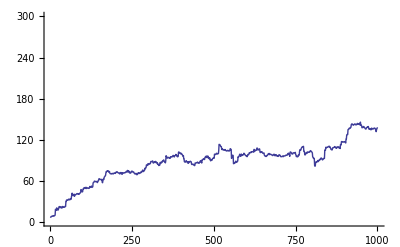

```mathematica
EvolvingMeanGraph=ListPlot[EvolvingMeanOfNetLevyDisplacements,PlotRange->{0,300},Joined->True]
```

```mathematica
Manipulate[Show[EvolvingMeanGraph,LevyPowerLaw[α]],{α,.5,1}]
```

The theoretical distribtion

ρ_Levi[x,y,N]

satisfies a "fractional diffusion equation"

1/2(∂_(x,x) +∂_(y,y))ρ=[∂_N]^f ρ

where [∂_N]^f is a "fractional derivative."

ADDENDUM: See the end of "Spectra of Random Matrices" (Notebook: 6 February 2010), where I record first encounter with the command

```mathematica
?RandomChoice
```

RandomChoice[{e_1,e_2,…}] gives a pseudorandom choice of one of the e_i. 
RandomChoice[list,n] gives a list of n pseudorandom choices. 
RandomChoice[list,{n_1,n_2,…}] gives an n_1×n_2×…  array of pseudorandom choices. 
RandomChoice[{w_1,w_2,…}->{e_1,e_2,…}] gives a pseudorandom choice weighted by the w_i. 
RandomChoice[wlist->elist,n] gives a list of n weighted choices.
RandomChoice[wlist->elist,{n_1,n_2,…}] gives an n_1×n_2×… array of weighted choices.

```mathematica
RandomChoice[{-1,+1},20]
```

{1,-1,-1,-1,1,1,-1,-1,1,-1,-1,1,-1,1,-1,1,-1,-1,1,-1}

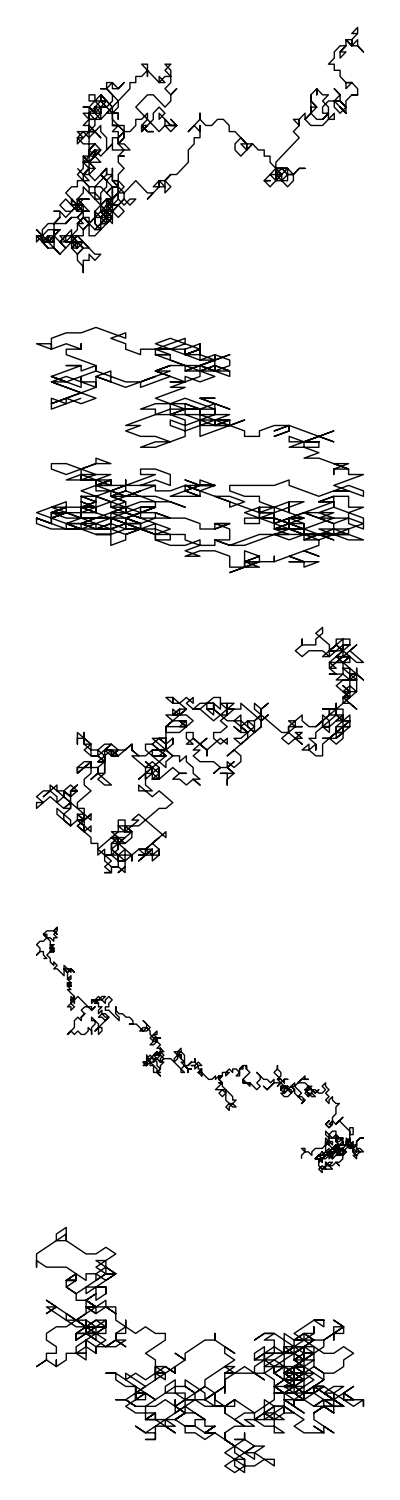

```mathematica
Table[Graphics[Line[Accumulate[RandomChoice[{-1,0,1},{1000,2}]]]],{k,1,5}]//TableForm
```

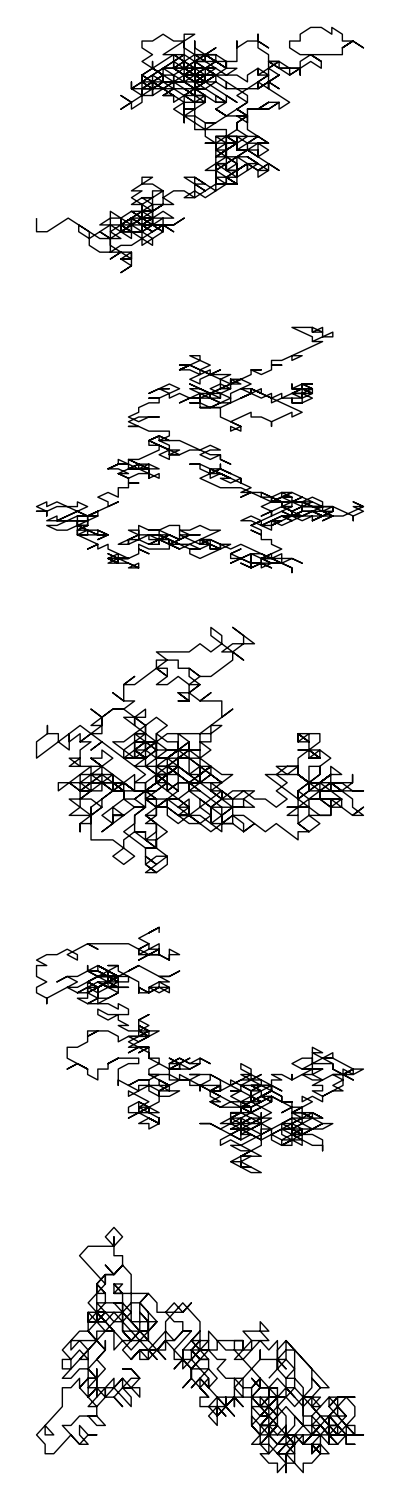

```mathematica
Table[Graphics[Line[Accumulate[RandomChoice[{-1,0,1},{1000,2}]]]],{k,1,5}]//TableForm
```

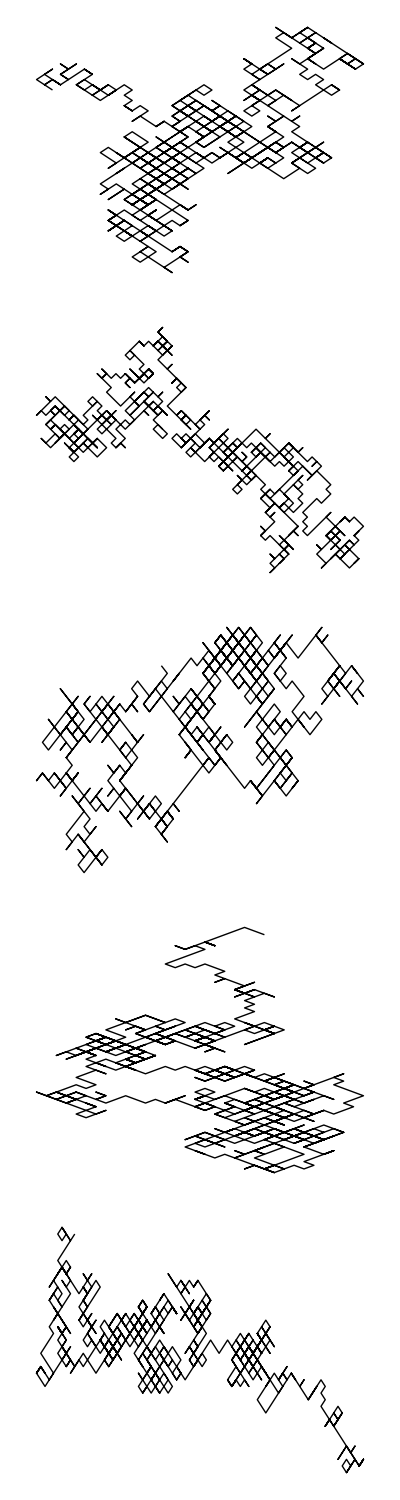

```mathematica
Table[Graphics[Line[Accumulate[RandomChoice[{-1,1},{1000,2}]]]],{k,1,5}]//TableForm
```

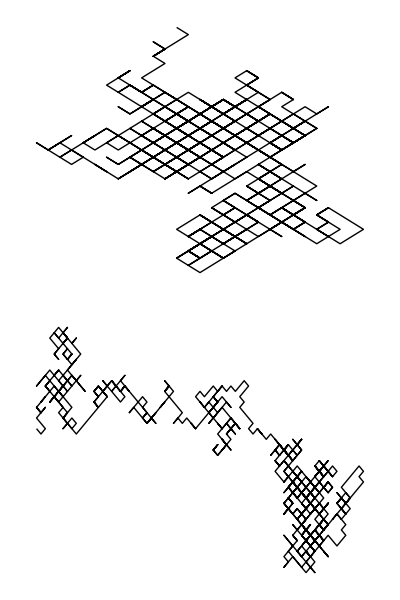

```mathematica
Table[Graphics[Line[Accumulate[RandomChoice[{-1,1},{1000,2}]]]],{k,1,2}]//TableForm
```

```mathematica
?Accumulate
```

Accumulate[list] gives a list of the successive accumulated totals of elements in list.

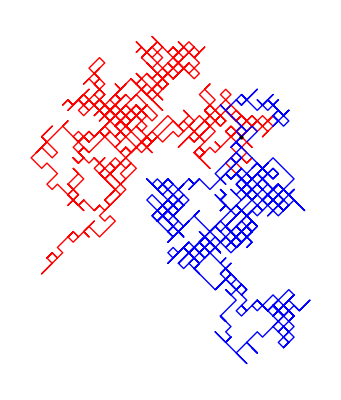

```mathematica
Graphics[{{Red,Line[Accumulate[RandomChoice[{-1,1},{1000,2}]]]},{Blue,Line[Accumulate[RandomChoice[{-1,1},{1000,2}]]]},{Point[{0,0}]}}]
```

```mathematica
RandomChoice[{-1,0,1},{10,2}]
```

{{0,-1},{0,-1},{0,0},{0,-1},{1,0},{1,0},{1,-1},{0,0},{0,-1},{1,1}}